# Auxiliary Functions

```mathematica
Quiet@Remove["Global`*"]
FormattingStrings[string_]:=Block[{},
auxiliarystring=StringReplace[string,"+ "->"+"];
auxiliarystring=StringReplace[auxiliarystring," +"->"+"];
auxiliarystring=StringReplace[auxiliarystring,"- "->"-"];
auxiliarystring=StringReplace[auxiliarystring," -"->"-"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot "->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\cdot"->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\right)"->"\\right)"];
auxiliarystring=StringReplace[auxiliarystring," "->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot"->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\times"->" \\times "];
auxiliarystring=ToExpression[auxiliarystring,TeXForm];
Return[auxiliarystring]
]
FormattingStringsCommaSplit[string_]:=Block[{},
auxiliarystring=StringReplace[string,"+ "->"+"];
auxiliarystring=StringReplace[auxiliarystring," +"->"+"];
auxiliarystring=StringReplace[auxiliarystring,"- "->"-"];
auxiliarystring=StringReplace[auxiliarystring," -"->"-"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot "->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\cdot"->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\right)"->"\\right)"];
auxiliarystring=StringReplace[auxiliarystring," "->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot"->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\times"->" \\times "];
auxiliarystring=StringSplit[auxiliarystring,","];
Return[auxiliarystring]
]
```

## Vector field and equilibrium point

```mathematica
SetDirectory[NotebookDirectory[]];
null[_String]:=Null;
eqbool=1;
If[FileExistsQ["Fixed parameter values.txt"],
Nparametereval=Length@ReadList["Fixed parameter values.txt",null@String,NullRecords->True];
,
Print["The file 'Fixed parameter values.txt' could not be found. Run the Python script first."];
Quit[];
]
If[Nparametereval>0,
For[parnum=1,parnum<=Nparametereval,parnum++,
aux=ReadLine["Fixed parameter values.txt"];
aux=FormattingStringsCommaSplit[aux];
parname=ToExpression[aux[[1]],TeXForm];
parval=ToExpression[aux[[2]],TeXForm];
parname//Evaluate=parval;
];
Close["Fixed parameter values.txt"];
]
ii[n_,x_]=√(π/(2x))*BesselI[n+1/2,x];
If[FileExistsQ["Kinetics.txt"],
nvar=Length@ReadList["Kinetics.txt",null@String,NullRecords->True];
,
Print["The file 'Kinetics.txt' could not found. Run the Python script first."];
Quit[];
]
nvar=nvar/2;
kinetics=Range[2*nvar];
var=Range[2*nvar];
For[varnum=1,varnum<=2*nvar,varnum++,
kinetics[[varnum]]=ReadLine["Kinetics.txt"];
kinetics[[varnum]]=FormattingStrings[kinetics[[varnum]]];
If[FileExistsQ["List of variables.txt"],
var[[varnum]]=ReadLine["List of variables.txt"];
,
Print["The file 'List of variables.txt' could not be found. Run the Python script first."];
Quit[]
];
var[[varnum]]=ToExpression[var[[varnum]],TeXForm];
];
Close["Kinetics.txt"];
Close["List of variables.txt"];
Bmatrix=-D[kinetics[[1;;nvar]],{var[[1;;nvar]]}];
Kmatrix=D[kinetics[[nvar+1;;2*nvar]],{var[[1;;nvar]]}];
Diffusionmatrix=Import["Diffusion matrix for Mathematica.json"];
Diffusionmatrix=ToExpression[Diffusionmatrix,TeXForm];
Diffbulk=Diffusionmatrix[[1;;nvar,1;;nvar]];
omega=DiagonalMatrix[Table[√((Bmatrix[[varnum]][[varnum]])/Diffbulk[[varnum,varnum]]),{varnum,nvar}]];
i0omegaR=DiagonalMatrix[Table[ii[0,omega[[varnum,varnum]]*R],{varnum,nvar}]];
i0primeomegaR=DiagonalMatrix[Table[D[ii[0,x],x]/.x->omega[[varnum,varnum]]*R,{varnum,nvar}]];
ilomegaR=DiagonalMatrix[Table[ii[l,omega[[varnum,varnum]]*R],{varnum,nvar}]];
ilprimeomegaR=DiagonalMatrix[Table[D[ii[l,x],x]/.x->omega[[varnum,varnum]]*R,{varnum,nvar}]];
S0=Dot[Inverse[Dot[Diffbulk,i0primeomegaR,omega]+Dot[Kmatrix,i0omegaR]],Kmatrix];
Sl=Dot[Inverse[Dot[Diffbulk,ilprimeomegaR,omega]+Dot[Kmatrix,ilomegaR]],Kmatrix];
If[eqbool==1,
eqs=Solve[kinetics[[nvar+1;;2*nvar]]==0/.Table[var[[varnum]]->i0omegaR[[varnum,varnum]]*S0[[varnum,varnum]]*var[[varnum+nvar]],{varnum,nvar}],var[[nvar+1;;2*nvar]]];
Print[eqs];
If[Length[eqs]>1,
eqnumber=Input["Enter the number of the equilibrium point you would like to consider. Enter 0 if the software did not find your desired homogeneous steady-state or you want to consider them all"];
If[eqnumber==0,
eq={0};
,
eq=eqs[[eqnumber]]//Simplify;]
,
eqnumber=1];
eq=eqs[[eqnumber]];
,
eq={0};
]
```

# Fixed parameters and Turing bifurcation variables

```mathematica
SetDirectory[NotebookDirectory[]];
lvalues={};
If[FileExistsQ["Values of l.txt"],
numberofl=Length@ReadList["Values of l.txt",null@String,NullRecords->True];
,
Print["The file 'Values of l.txt' could not be found. Run the Python script first."];
Quit[]
];
For[lnum=1,lnum<=numberofl,lnum++,
aux=ReadLine["Values of l.txt"];
AppendTo[lvalues,ToExpression[aux]];
];
zerodet=Range[numberofl];
For[counter=1,counter<=numberofl,counter++,
If[FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "/Determinant l=" <> ToString[lvalues[[counter]]] <> ".txt"],
zerodet[[counter]]=Import["l=" <> ToString[lvalues[[counter]]]<>"/Determinant l=" <> ToString[lvalues[[counter]]] <> ".txt"];
zerodet[[counter]]=FormattingStrings[zerodet[[counter]]];
,
Print["The file 'l= " <> ToString[lvalues[[counter]]]<>"/Determinant l= <> ToString[lvalues[[counter]]] <> .txt' could not be found. Run the Python script first."];
Quit[];
]
]
```

# Parameters on the axes of the bifurcation diagram

```mathematica
npar=2;
par=Range[npar];
lowerbound=Range[npar];
upperbound=Range[npar];
For[parnum=1,parnum<=npar,parnum++,
If[FileExistsQ["Parameters on axes.txt"],
aux=ReadLine["Parameters on axes.txt"];
,
Print["The file 'Parameters on axes.txt' could not be found. Run the Python script first."];
Quit[]
];
aux=FormattingStringsCommaSplit[aux];
par[[parnum]]=ToExpression[aux[[1]],TeXForm];
lowerbound[[parnum]]=ToExpression[aux[[2]],TeXForm];
upperbound[[parnum]]=ToExpression[aux[[3]],TeXForm];
]
Close["Parameters on axes.txt"];
If[FileExistsQ["Actual names of parameters.txt"],
aux=ReadLine["Actual names of parameters.txt"];
aux=FormattingStringsCommaSplit[aux];
newparam1=ToExpression[aux[[1]],TeXForm];
newparam2=ToExpression[aux[[2]],TeXForm];
Close["Actual names of parameters.txt"];
,
newparam1=par[[1]];
newparam2=par[[2]];
];
```

# Bifurcation curves

```mathematica
initialt=-1000;
finalt=1000;
curvespeed=1;
tol=10^-10;
simpleeq=0;
smalldifferential=0.001;
variabledependence=Table[var[[varnum]]->var[[varnum]][time],{varnum,2*nvar}];
kineticsaux=Table[var[[varnum]]-i0omegaR[[varnum,varnum]]*S0[[varnum,varnum]]*var[[varnum+nvar]],{varnum,nvar}]/.variabledependence/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time];
kineticsaux=Join[kineticsaux,kinetics[[nvar+1;;2*nvar]]/.variabledependence/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]];
solutioncurves=Range[Length[zerodet]];
allvar=Table[var[[varnum]],{varnum,2*nvar}];
AppendTo[allvar,par[[1]]];
AppendTo[allvar,par[[2]]];
allvartimedependent=Table[allvar[[varnum]][time],{varnum,Length[allvar]}];
For[counter=1,counter<=Length[zerodet],counter++,
zerodetaux=zerodet[[counter]]/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.variabledependence;
equations=Append[kineticsaux,zerodetaux];
equations=D[equations,time];
AppendTo[equations,(par[[1]]'[time])^2+(par[[2]]'[time])^2+∑_(varnum=1)^(2*nvar) (var[[varnum]]'[time])^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
If[FileExistsQ["Initial conditions for Turing bifurcation curves.txt"],
numberofbifurcationcurves=Length@ReadList["Initial conditions for Turing bifurcation curves.txt",null@String,NullRecords->True];
,
Print["The file 'Initial conditions for Turing bifurcation curves.txt' could not be found. Run the Python script first."];
Quit[];
];
initialvalueTuring={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
aux=ReadLine["Initial conditions for Turing bifurcation curves.txt"];
aux=FormattingStringsCommaSplit[aux];
AppendTo[initialvalueTuring,{ToExpression[aux[[1]],TeXForm],ToExpression[aux[[2]],TeXForm]}];
];
Close["Initial conditions for Turing bifurcation curves.txt"];
solutioncurves[[counter]]={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
fixedparameter=Position[par,initialvalueTuring[[bifnum]][[1]]][[1]][[1]];
If[fixedparameter==1,
anotherparameter=2;
,
anotherparameter=1;
];
If[simpleeq==1 && Length[eq]>1,initialvalues=Quiet@Chop[NSolve[zerodet[[counter]]==0/.eq/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],{par[[anotherparameter]]}//Evaluate],tol];
,
initialvalues=Quiet@Chop[NSolve[Join[{zerodet[[counter]]},kinetics[[nvar+1;;2*nvar]]/.Table[var[[varnum]]->i0omegaR[[varnum,varnum]]*S0[[varnum,varnum]]*var[[varnum+nvar]],{varnum,nvar}]]==0/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],Join[{par[[anotherparameter]]},var[[nvar+1;;2*nvar]]]//Evaluate],tol];
];
initialvalues=Table[Table[initialvalues[[initialsolnum]][[varnum]][[1]]->Re[initialvalues[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvalues[[initialsolnum]]]}],{initialsolnum,Length[initialvalues]}];
initialvalues=DeleteDuplicates[initialvalues];
For[initialsolnum=1,initialsolnum<=Length[initialvalues],initialsolnum++,
If[simpleeq==1 && Length[eq]>1,
AppendTo[initialvalues[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]];
initialvalues[[initialsolnum]]=Join[initialvalues[[initialsolnum]],Table[var[[varnum]]->(var[[varnum]]/.eq/.initialvalues[[initialsolnum]]),{varnum,2*nvar}]],
AppendTo[initialvalues[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]]
];
If[(par[[anotherparameter]]/.initialvalues[[initialsolnum]])∈Reals && If[Length[eq]>1,Norm[(var/.eq)-var/.initialvalues[[initialsolnum]]]<tol, True] && lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]]/.initialvalues[[initialsolnum]],
dereval=Table[par[[parnum]][0]->(par[[parnum]]/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]/.initialvalues[[initialsolnum]]),{parnum,npar}];
dereval=Join[dereval,Table[var[[varnum]][0]->(var[[varnum]]/.initialvalues[[initialsolnum]]),{varnum,2*nvar}]];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Append[equations,par[[fixedparameter]][0]==initialvalueTuring[[bifnum]][[2]]];
AppendTo[equationsaux,par[[anotherparameter]][0]==(par[[anotherparameter]]/.initialvalues[[initialsolnum]])];
equationsaux=Join[equationsaux,Table[var[[varnum]][0]==(var[[varnum]]/.initialvalues[[initialsolnum]]),{varnum,nvar+1,2*nvar}]];
equationsaux=Join[equationsaux,Table[var[[varnum]]'[0]==(var[[varnum]]'[0]/.initialderivatives[[dernumber]]),{varnum,nvar+1,2*nvar}]];
equationsaux=Join[equationsaux,Table[par[[parnum]]'[0]==(par[[parnum]]'[0]/.initialderivatives[[dernumber]]),{parnum,npar}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]<=lowerbound[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]>=upperbound[[1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]<=lowerbound[[2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]>=upperbound[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[Length[sol]>0&& sol[[1]][[1]][[2]]["Domain"][[1]][[1]]<sol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurves[[counter]],sol];
]
]
]
]
]
]
If[Length[solutioncurves]==0,Print["This script could not find a Turing bifurcation curve nor a BD-line for your desired parameters. Try changing the integration method."]]
```

# Bifurcation diagram plotting

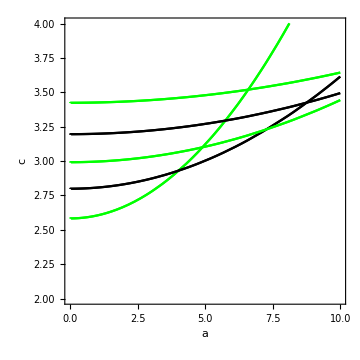

```mathematica
If[ValueQ[critchange] && Length[critchange]>=1,
critpoints=Table[Graphics[{PointSize[0.02],Point[{par[[1]],par[[2]]}/.critchange[[critnum]][[2]]]}],{critnum,Length[critchange]}];
]
bifcurveplot=Range[Length[zerodet]];
For[counter=1,counter<=Length[zerodet],counter++,
bifcurveplot[[counter]]={};
For[outersolnum=1,outersolnum<=Length[solutioncurves[[counter]]],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[counter]][[outersolnum]]],innersolnum++,
If[OddQ[lvalues[[counter]]],
tempplot=Quiet@ParametricPlot[{par[[1]][time],par[[2]][time]}/. solutioncurves[[counter]][[outersolnum]][[innersolnum]],{time,solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Green,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}},PlotLabel->"l=" <> ToString[lvalues[[counter]]]];
,
tempplot=Quiet@ParametricPlot[{par[[1]][time],par[[2]][time]}/. solutioncurves[[counter]][[outersolnum]][[innersolnum]],{time,solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Black,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}},PlotLabel->"l=" <> ToString[lvalues[[counter]]]];
];
AppendTo[bifcurveplot[[counter]],tempplot];
]
]
]
If[ValueQ[critpoints] && Length[critpoints]>0,
Row[(Show[#1,critpoints,ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]&)/@Flatten[bifcurveplot,0]];
Show[bifcurveplot,critpoints,PlotLabel->"",ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
,
Row[(Show[#1,ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]&)/@Flatten[bifcurveplot,0]];
Show[bifcurveplot,PlotLabel->"",ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
]
```

# Getting points

```mathematica
parnum=1;
parval=4.3;
fixed={par[[parnum]]->parval};
actualt=Range[Length[zerodet]];
evaluations=Range[Length[zerodet]];
For[counter=1,counter<=Length[zerodet],counter++,
actualt[[counter]]={};
evaluations[[counter]]={};
For [outersolnum=1,outersolnum<=Length[solutioncurves[[counter]]],outersolnum++,
For [innersolnum=1,innersolnum<=Length[solutioncurves[[counter]][[outersolnum]]],innersolnum++,
tguess=Quiet@NSolve[par[[parnum]][time]-parval==0/.solutioncurves[[counter]][[outersolnum]][[innersolnum]],time];
For[solnum=1,solnum<=Length[tguess],solnum++,
If[Abs[par[[parnum]][time]-parval/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]]]<tol,
AppendTo[actualt[[counter]],tguess];
AppendTo[evaluations[[counter]],Join[{par[[1]]->(par[[1]][time]/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]]),par[[2]]->(par[[2]][time]/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]])},
Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]]),{varnum,2*nvar}]]]
]
]
]
]
]
```

# Amplitude equations

```mathematica
If[FileExistsQ["Crosspar.txt"],
crosspar=Import["Crosspar.txt"];
crosspar=ToExpression[crosspar,TeXForm];
]
amplitudeequations=Range[Length[zerodet]];
For[counter=1,counter<=Length[zerodet],counter++,
amplitudeequations[[counter]]=ConstantArray[0,2*lvalues[[counter]]+1];
For[mval=-lvalues[[counter]],mval<=lvalues[[counter]],mval++,
For[Subscript[q, 1]=-lvalues[[counter]],Subscript[q, 1]<=lvalues[[counter]],Subscript[q, 1]++,
For[Subscript[q, 2]=-lvalues[[counter]],Subscript[q, 2]<=lvalues[[counter]],Subscript[q, 2]++,
If[EvenQ[lvalues[[counter]]] && FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//C2 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", m=" <> ToString[mval] <> ".txt"],
C2=Import["l=" <> ToString[lvalues[[counter]]] <> "//C2 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", m=" <> ToString[mval] <> ".txt"];
C2expression=FormattingStrings[C2]/.evaluations[[counter]][[1]];
amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]=amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]+C2expression*ToExpression["A_{" <> ToString[Subscript[q, 1]] <> "} \\times A_{" <> ToString[Subscript[q, 2]] <> "}",TeXForm];
,
For[Subscript[q, 3]=-lvalues[[counter]],Subscript[q, 3]<=lvalues[[counter]],Subscript[q, 3]++,
If[FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//C3 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", q3=" <> ToString[Subscript[q, 3]] <> ", m=" <> ToString[mval] <> ".txt"],
C3=Import["l=" <> ToString[lvalues[[counter]]] <> "//C3 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", q3=" <> ToString[Subscript[q, 3]] <> ", m=" <> ToString[mval] <> ".txt"];
C3expression=FormattingStrings[C3]/.evaluations[[counter]][[1]];
amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]=amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]+C3expression*ToExpression["A_{" <> ToString[Subscript[q, 1]] <> "} \\times A_{" <> ToString[Subscript[q, 2]] <> "} \\times A_{" <> ToString[Subscript[q, 3]] <> "}",TeXForm];
]
]
]
]
];
If[FileExistsQ["Crosspar.txt"] && FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//Cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"],
C11=Import["l=" <> ToString[lvalues[[counter]]] <> "//Cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"];
C11=FormattingStrings[C11];
amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]=amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]+(crossval-crosspar)*C11*ToExpression["A_{" <> ToString[mval] <> "}",TeXForm]/.evaluations[[counter]][[1]];
,
If[mval>=0,
amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]=amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]+ϵ*ToExpression["A_{" <> ToString[mval] <> "}",TeXForm]
]
]
];
If[EvenQ[lvalues[[counter]]],
negativem=Table[Subscript[A, -m]->Subscript[B, m],{m,1,lvalues[[counter]]}];
positivem=Table[Subscript[A, m]->Subscript[A, -m],{m,1,lvalues[[counter]]}];
recover=Table[Subscript[B, m]->Subscript[A, m],{m,1,lvalues[[counter]]}];
For[eqnum=1,eqnum<=lvalues[[counter]],eqnum++,
amplitudeequations[[counter]][[eqnum]]=amplitudeequations[[counter]][[2*lvalues[[counter]]+1-(eqnum-1)]]/.negativem/.positivem/.recover;
]
]
]
```

```mathematica
crossval=3.0;
amplitudeequilibria=Range[Length[zerodet]];
jacmat=Range[Length[zerodet]];
For[counter=1,counter<=Length[zerodet],counter++,
amplitudeequilibria[[counter]]=NSolve[Join[amplitudeequations[[counter]]==0/.Table[Subscript[A, -m]->Subscript[A, m],{m,1,lvalues[[counter]]}]],Table[Subscript[A, m],{m,0,lvalues[[counter]]}]]//Simplify;
jacmat[[counter]]=D[amplitudeequations[[counter]][[lvalues[[counter]]+1;;2*lvalues[[counter]]+1]]/.Table[Subscript[A, -m]->Subscript[A, m],{m,1,lvalues[[counter]]}],{Table[Subscript[A, m],{m,0,lvalues[[counter]]}]}];
]
```

```mathematica
For[counter=1,counter<=Length[zerodet],counter++,
For[eqnum=1,eqnum<=Length[amplitudeequilibria[[counter]]],eqnum++,
If[Max[Re[Eigenvalues[jacmat[[counter]]/.Table[Subscript[A, -m]->Subscript[A, m],{m,1,lvalues[[counter]]}]/.amplitudeequilibria[[counter]][[eqnum]]]]]<0,Print[ToString[counter] <> "," <> ToString[eqnum]]]
]
]
```

3,15

4,32

5,19

```mathematica
counter=3;
eqnum=15;
amplitudeequilibria[[counter]][[eqnum]]
Eigenvalues[jacmat[[counter]]/.Table[Subscript[A, -m]->Subscript[A, m],{m,1,lvalues[[counter]]}]/.amplitudeequilibria[[counter]][[eqnum]]]
```

{A_0→0.,A_1→0.,A_2→0.,A_3→0.}

{-0.0719487,-0.0719487,-0.0719487,-0.0719487}